```mathematica
Quit[];
```

```mathematica
eq1=f'[r]+(-4 ep+4 f[r]+2 r^2 V[ph[r]]+r^2 f[r] ph'[r]^2)/(4 r);
eq2=(2 ep ph'[r]+2 f[r] ph'[r]-r^2 V[ph[r]] ph'[r]-2 r V'[ph[r]])/(2 r f[r])+ph''[r];
eq3=h'[r]-(h[r] (4 ep-2 r^2 V[ph[r]]+f[r] (-4+r^2 ph'[r]^2)))/(4 r f[r]);
V[x_]:=-g5 x^5 -g7 x^7;
ep=1;
```

```mathematica
repftoff={f[r]->1 + ff[r]/r};
repftoff=Join[repftoff,D[repftoff,r]];
eqq1=eq1/.repftoff//Simplify;eqq2=eq2/.repftoff//Simplify;eqq3=eq3/.repftoff//Simplify;
```

```mathematica
(* f[r_]:=1+ff1/r + ff2/r^2 + ff3/r^3;
h[r_]:=1 + hh1/r + hh2/r^2 + hh3/r^3;
ph[r_]:=pp1/r + pp2/r^2 + pp3/r^3;
ep=1;
hh1=ff1;
ff2=pp1^2/4;hh2=0;pp2=1/2 (-ff1 pp1-5 g5 pp1^4);
ff3=1/8 (-ff1 pp1^2-12 g5 pp1^5);hh3=1/24 (-ff1 pp1^2+4 g5 pp1^5);pp3=1/24 (8 ff1^2 pp1-pp1^3+80 ff1 g1 pp1^4+200 g5^2 pp1^7); *)
```

```mathematica
iff[r_]:=r(if[r]-1);
if[r_]:=f1 (r-r0)  + f2 (r-r0)^2 + f3 (r-r0)^3 + f4 (r-r0)^4 + f5(r-r0)^5
iph[r_]:=p0 + p1 (r-r0)  + p2 (r-r0)^2 + p3 (r-r0)^3 + p4 (r-r0)^4 + p5 (r-r0)^5;
ih[r_]:=(r-r0)  + h2 (r-r0)^2 + h3 (r-r0)^3 + h4 (r-r0)^4 + h5 (r-r0)^5;
f1=1/r0+1/2 p0^5 (g5+g7 p0^2) r0;p1=-(2 p0^4 (5 g5+7 g7 p0^2) r0)/(2+g5 p0^5 r0^2+g7 p0^7 r0^2);
h2=(-8-4 g7 p0^7 r0^2+25 g5^2 p0^8 r0^4+49 g7^2 p0^12 r0^4+2 g5 p0^5 r0^2 (-2+35 g7 p0^5 r0^2))/(2 r0 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^2);f2=-((8+4 g5 p0^5 r0^2+4 g7 p0^7 r0^2+75 g5^2 p0^8 r0^4+210 g5 g7 p0^10 r0^4+147 g7^2 p0^12 r0^4)/(8 r0^2+4 g5 p0^5 r0^4+4 g7 p0^7 r0^4));p2=(p0^7 (5 g5+7 g7 p0^2) r0^2 (g5^2 p0^5 (-5+p0^2) r0^2+g7 p0^2 (84+2 p0^2-7 g7 p0^7 r0^2+g7 p0^9 r0^2)+2 g5 (20+p0^2-4 g7 p0^7 r0^2+g7 p0^9 r0^2)))/(2+g5 p0^5 r0^2+g7 p0^7 r0^2)^3;
h3=1/(6 r0^2 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^4)(96+160 g7 p0^7 r0^2+4 g7^2 p0^12 (-343+24 p0^2) r0^4+4 g7^3 p0^17 (-2058-245 p0^2+6 p0^4) r0^6+g7^4 p0^24 (3087-147 p0^2+2 p0^4) r0^8+g5^4 p0^16 (875-75 p0^2+2 p0^4) r0^8+4 g5^3 p0^11 r0^6 (-500-125 p0^2+6 p0^4+1150 g7 p0^7 r0^2-90 g7 p0^9 r0^2+2 g7 p0^11 r0^2)+2 g5^2 p0^8 r0^4 (-350+48 p0^2-4900 g7 p0^5 r0^2-950 g7 p0^7 r0^2+36 g7 p0^9 r0^2+4655 g7^2 p0^12 r0^4-321 g7^2 p0^14 r0^4+6 g7^2 p0^16 r0^4)+4 g5 p0^5 r0^2 (40+2 g7 p0^5 (-245+24 p0^2) r0^2+g7^2 p0^10 (-3920-595 p0^2+18 p0^4) r0^4+2 g7^3 p0^17 (1078-63 p0^2+p0^4) r0^6));f3=1/(12 r0^3 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^3)(96+160 g7 p0^7 r0^2+4 g7^2 p0^12 (-49+24 p0^2) r0^4+4 g7^3 p0^17 (10290+49 p0^2+6 p0^4) r0^6+g5^4 p0^16 (3125+75 p0^2+2 p0^4) r0^8+g7^4 p0^24 (13377+147 p0^2+2 p0^4) r0^8+4 g5^3 p0^11 r0^6 (2500+25 p0^2+6 p0^4+4750 g7 p0^7 r0^2+90 g7 p0^9 r0^2+2 g7 p0^11 r0^2)+2 g5^2 p0^8 r0^4 (-50+48 p0^2+24500 g7 p0^5 r0^2+190 g7 p0^7 r0^2+36 g7 p0^9 r0^2+20825 g7^2 p0^12 r0^4+321 g7^2 p0^14 r0^4+6 g7^2 p0^16 r0^4)+4 g5 p0^5 r0^2 (40+2 g7 p0^5 (-35+24 p0^2) r0^2+g7^2 p0^10 (19600+119 p0^2+18 p0^4) r0^4+2 g7^3 p0^17 (4900+63 p0^2+p0^4) r0^6));p3=-1/(9 r0 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^5)p0^4 (5 g5^5 p0^16 (125-30 p0^2+6 p0^4) r0^8+g5^4 p0^11 r0^6 (-35000+2750 p0^2+140 p0^4+3325 g7 p0^7 r0^2-750 g7 p0^9 r0^2+162 g7 p0^11 r0^2)+2 g5^3 p0^6 r0^4 (20000+2650 p0^2+120 p0^4-95850 g7 p0^7 r0^2+7450 g7 p0^9 r0^2+308 g7 p0^11 r0^2+2935 g7^2 p0^14 r0^4-798 g7^2 p0^16 r0^4+174 g7^2 p0^18 r0^4)+2 g5^2 p0^3 r0^2 (-800+120 p0^2+120400 g7 p0^5 r0^2+11250 g7 p0^7 r0^2+408 g7 p0^9 r0^2-207410 g7^2 p0^12 r0^4+14720 g7^2 p0^14 r0^4+504 g7^2 p0^16 r0^4+2023 g7^3 p0^19 r0^6-918 g7^3 p0^21 r0^6+186 g7^3 p0^23 r0^6)+7 g7 p0^2 (32+48 g7 p0^5 (-14+p0^2) r0^2+12 g7^2 p0^10 (3136+175 p0^2+4 p0^4) r0^4+14 g7^3 p0^17 (-1722+81 p0^2+2 p0^4) r0^6+3 g7^4 p0^24 (49-14 p0^2+2 p0^4) r0^8)+g5 (160+32 g7 p0^5 (-175+18 p0^2) r0^2+4 g7^2 p0^10 (111720+7903 p0^2+228 p0^4) r0^4+28 g7^3 p0^17 (-15057+901 p0^2+26 p0^4) r0^6+3 g7^4 p0^24 (539-378 p0^2+66 p0^4) r0^8));
h4=-1/(72 r0^3 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^6)(4608+12288 g7 p0^7 r0^2+896 g7^2 p0^12 (-56+15 p0^2) r0^4+192 g7^3 p0^17 (-4802-539 p0^2+40 p0^4) r0^6-12 g7^4 p0^22 (480200+31899 p0^2+6174 p0^4-200 p0^6) r0^8+8 g7^5 p0^29 (792330+20580 p0^2-2695 p0^4+48 p0^6) r0^10+3 g7^6 p0^36 (-228095+20923 p0^2-686 p0^4+8 p0^6) r0^12+g5^6 p0^24 (-113125+17625 p0^2-1050 p0^4+24 p0^6) r0^12+2 g5^5 p0^19 r0^10 (430000+26000 p0^2-5500 p0^4+192 p0^6-431625 g7 p0^7 r0^2+64275 g7 p0^9 r0^2-3570 g7 p0^11 r0^2+72 g7 p0^13 r0^2)+g5^4 p0^14 r0^8 (-640000-78500 p0^2-37800 p0^4+2400 p0^6+6262000 g7 p0^7 r0^2+304800 g7 p0^9 r0^2-63800 g7 p0^11 r0^2+1920 g7 p0^13 r0^2-2788675 g7^2 p0^14 r0^4+393855 g7^2 p0^16 r0^4-20118 g7^2 p0^18 r0^4+360 g7^2 p0^20 r0^4)+4 g5^3 p0^11 r0^6 (-56000-13200 p0^2+1920 p0^4-1162000 g7 p0^5 r0^2-132100 g7 p0^7 r0^2-45360 g7 p0^9 r0^2+2400 g7 p0^11 r0^2+4610200 g7^2 p0^12 r0^4+184720 g7^2 p0^14 r0^4-36740 g7^2 p0^16 r0^4+960 g7^2 p0^18 r0^4-1227135 g7^3 p0^19 r0^6+162093 g7^3 p0^21 r0^6-7518 g7^3 p0^23 r0^6+120 g7^3 p0^25 r0^6)+g5^2 p0^8 r0^4 (-25600+13440 p0^2-1097600 g7 p0^5 r0^2-200640 g7 p0^7 r0^2+23040 g7 p0^9 r0^2-12191200 g7^2 p0^10 r0^4-1213240 g7^2 p0^12 r0^4-323568 g7^2 p0^14 r0^4+14400 g7^2 p0^16 r0^4+27487040 g7^3 p0^17 r0^6+931392 g7^3 p0^19 r0^6-168080 g7^3 p0^21 r0^6+3840 g7^3 p0^23 r0^6-4997755 g7^4 p0^24 r0^8+604023 g7^4 p0^26 r0^8-25158 g7^4 p0^28 r0^8+360 g7^4 p0^30 r0^8)+2 g5 p0^5 r0^2 (6144+4480 g7 p0^5 (-8+3 p0^2) r0^2+32 g7^2 p0^10 (-27440-3927 p0^2+360 p0^4) r0^4+8 g7^3 p0^15 (-864360-71981 p0^2-15876 p0^4+600 p0^6) r0^6+4 g7^4 p0^22 (2593080+76244 p0^2-11935 p0^4+240 p0^6) r0^8+3 g7^5 p0^29 (-468195+50225 p0^2-1862 p0^4+24 p0^6) r0^10));f4=-1/(144 r0^4 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^5)(4608+12288 g7 p0^7 r0^2+4480 g7^2 p0^12 (7+3 p0^2) r0^4+384 g7^3 p0^17 (-1715+147 p0^2+20 p0^4) r0^6+12 g7^4 p0^22 (3361400+27097 p0^2+3626 p0^4+200 p0^6) r0^8+8 g7^5 p0^29 (2319366+69972 p0^2+2107 p0^4+48 p0^6) r0^10+3 g7^6 p0^36 (789929+38759 p0^2+882 p0^4+8 p0^6) r0^12+g5^6 p0^24 (191875+28125 p0^2+1350 p0^4+24 p0^6) r0^12+2 g5^5 p0^19 r0^10 (890000+70000 p0^2+4300 p0^4+192 p0^6+1086375 g7 p0^7 r0^2+111375 g7 p0^9 r0^2+4590 g7 p0^11 r0^2+72 g7 p0^13 r0^2)+g5^4 p0^14 r0^8 (4480000+87500 p0^2+22200 p0^4+2400 p0^6+16226000 g7 p0^7 r0^2+948000 g7 p0^9 r0^2+49880 g7 p0^11 r0^2+1920 g7 p0^13 r0^2+8978725 g7^2 p0^14 r0^4+721275 g7^2 p0^16 r0^4+25866 g7^2 p0^18 r0^4+360 g7^2 p0^20 r0^4)+4 g5^3 p0^11 r0^6 (-40000+7200 p0^2+1920 p0^4+8134000 g7 p0^5 r0^2+119500 g7 p0^7 r0^2+26640 g7 p0^9 r0^2+2400 g7 p0^11 r0^2+13592600 g7^2 p0^12 r0^4+633200 g7^2 p0^14 r0^4+28724 g7^2 p0^16 r0^4+960 g7^2 p0^18 r0^4+4562145 g7^3 p0^19 r0^6+306225 g7^3 p0^21 r0^6+9666 g7^3 p0^23 r0^6+120 g7^3 p0^25 r0^6)+g5^2 p0^8 r0^4 (16000+13440 p0^2-784000 g7 p0^5 r0^2+109440 g7 p0^7 r0^2+23040 g7 p0^9 r0^2+85338400 g7^2 p0^10 r0^4+989800 g7^2 p0^12 r0^4+190032 g7^2 p0^14 r0^4+14400 g7^2 p0^16 r0^4+85832320 g7^3 p0^17 r0^6+3339840 g7^3 p0^19 r0^6+131408 g7^3 p0^21 r0^6+3840 g7^3 p0^23 r0^6+19672765 g7^4 p0^24 r0^8+1152627 g7^4 p0^26 r0^8+32346 g7^4 p0^28 r0^8+360 g7^4 p0^30 r0^8)+2 g5 p0^5 r0^2 (6144+4480 g7 p0^5 (5+3 p0^2) r0^2+64 g7^2 p0^10 (-9800+1071 p0^2+180 p0^4) r0^4+8 g7^3 p0^15 (6050520+57575 p0^2+9324 p0^4+600 p0^6) r0^6+4 g7^4 p0^22 (8067360+271852 p0^2+9331 p0^4+240 p0^6) r0^8+3 g7^5 p0^29 (1798349+95109 p0^2+2394 p0^4+24 p0^6) r0^10));p4=1/(36 r0^2 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^7)p0^4 (5 g5^7 p0^24 (1375+150 p0^2-75 p0^4+18 p0^6) r0^12+g5^6 p0^19 r0^10 (1885000-253250 p0^2+11650 p0^4+720 p0^6+56125 g7 p0^7 r0^2+4950 g7 p0^9 r0^2-2625 g7 p0^11 r0^2+666 g7 p0^13 r0^2)+g5^5 p0^14 r0^8 (-8480000+222500 p0^2+41500 p0^4+2640 p0^6+14525500 g7 p0^7 r0^2-1883800 g7 p0^9 r0^2+86100 g7 p0^11 r0^2+4608 g7 p0^13 r0^2+206275 g7^2 p0^14 r0^4+8130 g7^2 p0^16 r0^4-8115 g7^2 p0^18 r0^4+2106 g7^2 p0^20 r0^4)+g5^4 p0^9 r0^6 (3680000+1328000 p0^2+17400 p0^4+6000 p0^6-66384000 g7 p0^7 r0^2+2081900 g7 p0^9 r0^2+260300 g7 p0^11 r0^2+14256 g7 p0^13 r0^2+47382900 g7^2 p0^14 r0^4-5961490 g7^2 p0^16 r0^4+261046 g7^2 p0^18 r0^4+12240 g7^2 p0^20 r0^4+494685 g7^3 p0^21 r0^6-8022 g7^3 p0^23 r0^6-14445 g7^3 p0^25 r0^6+3690 g7^3 p0^27 r0^6)+g5^3 p0^6 r0^4 (-272000-25600 p0^2+8640 p0^4+32704000 g7 p0^5 r0^2+8301600 g7 p0^7 r0^2+91200 g7 p0^9 r0^2+26400 g7 p0^11 r0^2-210781200 g7^2 p0^12 r0^4+6762840 g7^2 p0^14 r0^4+645720 g7^2 p0^16 r0^4+30624 g7^2 p0^18 r0^4+84819560 g7^3 p0^19 r0^6-10264896 g7^3 p0^21 r0^6+416456 g7^3 p0^23 r0^6+17280 g7^3 p0^25 r0^6+850521 g7^4 p0^26 r0^8-37614 g7^4 p0^28 r0^8-16005 g7^4 p0^30 r0^8+3870 g7^4 p0^32 r0^8)+g5^2 p0^3 r0^2 (12800+6720 p0^2-1624000 g7 p0^5 r0^2-105600 g7 p0^7 r0^2+29376 g7 p0^9 r0^2+98431200 g7^2 p0^10 r0^4+19286400 g7^2 p0^12 r0^4+177456 g7^2 p0^14 r0^4+43200 g7^2 p0^16 r0^4-339742480 g7^3 p0^17 r0^6+10072552 g7^3 p0^19 r0^6+792376 g7^3 p0^21 r0^6+32736 g7^3 p0^23 r0^6+89434016 g7^4 p0^24 r0^8-10111206 g7^4 p0^26 r0^8+369342 g7^4 p0^28 r0^8+13680 g7^4 p0^30 r0^8+928991 g7^5 p0^31 r0^10-40950 g7^5 p0^33 r0^10-10995 g7^5 p0^35 r0^10+2430 g7^5 p0^37 r0^10)+7 g7 p0^2 (384+1344 g7 p0^5 (4+p0^2) r0^2+64 g7^2 p0^10 (-3969-154 p0^2+27 p0^4) r0^4+24 g7^3 p0^15 (333396+45080 p0^2+287 p0^4+50 p0^6) r0^6+12 g7^4 p0^22 (-1093484+21903 p0^2+1379 p0^4+44 p0^6) r0^8+2 g7^5 p0^29 (1026942-85701 p0^2+2387 p0^4+72 p0^6) r0^10+3 g7^6 p0^36 (4459-98 p0^2-35 p0^4+6 p0^6) r0^12)+g5 (1920+1792 g7 p0^5 (25+9 p0^2) r0^2+64 g7^2 p0^10 (-47040-2296 p0^2+513 p0^4) r0^4+32 g7^3 p0^15 (3869040+618233 p0^2+4746 p0^4+975 p0^6) r0^6+4 g7^4 p0^22 (-69424572+1754641 p0^2+120323 p0^4+4356 p0^6) r0^8+4 g7^5 p0^29 (13396551-1344266 p0^2+43225 p0^4+1440 p0^6) r0^10+3 g7^6 p0^36 (171843-5782 p0^2-1435 p0^4+282 p0^6) r0^12));
h5=1/(360 r0^4 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^8)(92160+337920 g7 p0^7 r0^2+8960 g7^2 p0^12 (-119+60 p0^2) r0^4+896 g7^3 p0^17 (-13524-3451 p0^2+540 p0^4) r0^6+336 g7^4 p0^22 (-768320-89621 p0^2-11270 p0^4+800 p0^6) r0^8+1568 g7^5 p0^27 (-1092798+14994 p0^2-10983 p0^4-1573 p0^6+60 p0^8) r0^10+56 g7^6 p0^34 (66037104+3330873 p0^2+18228 p0^4-15806 p0^6+360 p0^8) r0^12+24 g7^7 p0^41 (-51782367+1659091 p0^2+111132 p0^4-6762 p0^6+100 p0^8) r0^14+5 g5^8 p0^32 (1114375-248250 p0^2+23925 p0^4-1170 p0^6+24 p0^8) r0^16+3 g7^8 p0^48 (18605349-2549862 p0^2+143031 p0^4-3822 p0^6+40 p0^8) r0^16+20 g5^7 p0^27 r0^14 (-4867500+226750 p0^2+39050 p0^4-4140 p0^6+120 p0^8+2778625 g7 p0^7 r0^2-601350 g7 p0^9 r0^2+55755 g7 p0^11 r0^2-2574 g7 p0^13 r0^2+48 g7 p0^15 r0^2)+8 g5^6 p0^22 r0^12 (29100000+3234375 p0^2+77750 p0^4-56450 p0^6+2520 p0^8-117151875 g7 p0^7 r0^2+5657125 g7 p0^9 r0^2+794050 g7 p0^11 r0^2-80730 g7 p0^13 r0^2+2100 g7 p0^15 r0^2+30620875 g7^2 p0^14 r0^4-6421725 g7^2 p0^16 r0^4+570270 g7^2 p0^18 r0^4-24687 g7^2 p0^20 r0^4+420 g7^2 p0^22 r0^4)+4 g5^5 p0^17 r0^10 (-21200000+2340000 p0^2-948000 p0^4-314600 p0^6+23520 p0^8+552630000 g7 p0^7 r0^2+52762500 g7 p0^9 r0^2+807700 g7 p0^11 r0^2-767720 g7 p0^13 r0^2+30240 g7 p0^15 r0^2-977689500 g7^2 p0^14 r0^4+47702450 g7^2 p0^16 r0^4+5591510 g7^2 p0^18 r0^4-537372 g7^2 p0^20 r0^4+12600 g7^2 p0^22 r0^4+156272225 g7^3 p0^21 r0^6-31642110 g7^3 p0^23 r0^6+2673591 g7^3 p0^25 r0^6-107874 g7^3 p0^27 r0^6+1680 g7^3 p0^29 r0^6)+2 g5^4 p0^14 r0^8 (-14320000-3605000 p0^2-966000 p0^4+134400 p0^6-417760000 g7 p0^5 r0^2+20376000 g7 p0^7 r0^2-13964400 g7 p0^9 r0^2-3649360 g7 p0^11 r0^2+235200 g7 p0^13 r0^2+4367832000 g7^2 p0^12 r0^4+362518500 g7^2 p0^14 r0^4+3511040 g7^2 p0^16 r0^4-4326328 g7^2 p0^18 r0^4+151200 g7^2 p0^20 r0^4-4594974300 g7^3 p0^19 r0^6+220471420 g7^3 p0^21 r0^6+22088128 g7^3 p0^23 r0^6-1978920 g7^3 p0^25 r0^6+42000 g7^3 p0^27 r0^6+506983435 g7^4 p0^26 r0^8-98512830 g7^4 p0^28 r0^8+7850037 g7^4 p0^30 r0^8-293670 g7^4 p0^32 r0^8+4200 g7^4 p0^34 r0^8)+4 g5^3 p0^11 r0^6 (-736000-394400 p0^2+120960 p0^4-52052000 g7 p0^5 r0^2-10754000 g7 p0^7 r0^2-2318400 g7 p0^9 r0^2+268800 g7 p0^11 r0^2-782726000 g7^2 p0^10 r0^4+16237200 g7^2 p0^12 r0^4-19552320 g7^2 p0^14 r0^4-4203056 g7^2 p0^16 r0^4+235200 g7^2 p0^18 r0^4+4606627200 g7^3 p0^17 r0^6+335634600 g7^3 p0^19 r0^6+2194648 g7^3 p0^21 r0^6-3233456 g7^3 p0^23 r0^6+100800 g7^3 p0^25 r0^6-3291750420 g7^4 p0^24 r0^8+150726170 g7^4 p0^26 r0^8+13202174 g7^4 p0^28 r0^8-1088820 g7^4 p0^30 r0^8+21000 g7^4 p0^32 r0^8+269200463 g7^5 p0^31 r0^10-49671594 g7^5 p0^33 r0^10+3692589 g7^5 p0^35 r0^10-127530 g7^5 p0^37 r0^10+1680 g7^5 p0^39 r0^10)+8 g5^2 p0^8 r0^4 (-68000+67200 p0^2-1803200 g7 p0^5 r0^2-749360 g7 p0^7 r0^2+181440 g7 p0^9 r0^2-68286400 g7^2 p0^10 r0^4-11676700 g7^2 p0^12 r0^4-2067240 g7^2 p0^14 r0^4+201600 g7^2 p0^16 r0^4-707334600 g7^3 p0^15 r0^6+7120680 g7^3 p0^17 r0^6-13146504 g7^3 p0^19 r0^6-2403544 g7^3 p0^21 r0^6+117600 g7^3 p0^23 r0^6+2738292480 g7^4 p0^22 r0^8+176316945 g7^4 p0^24 r0^8+915614 g7^4 p0^26 r0^8-1352542 g7^4 p0^28 r0^8+37800 g7^4 p0^30 r0^8-1441082601 g7^5 p0^29 r0^10+60884803 g7^5 p0^31 r0^10+4767994 g7^5 p0^33 r0^10-358110 g7^5 p0^35 r0^10+6300 g7^5 p0^37 r0^10+92083152 g7^6 p0^36 r0^12-15852921 g7^6 p0^38 r0^12+1086183 g7^6 p0^40 r0^12-34515 g7^6 p0^42 r0^12+420 g7^6 p0^44 r0^12)+4 g5 p0^5 r0^2 (84480+22400 g7 p0^5 (-17+12 p0^2) r0^2+224 g7^2 p0^10 (-25760-8381 p0^2+1620 p0^4) r0^4+560 g7^3 p0^15 (-276654-39179 p0^2-5796 p0^4+480 p0^6) r0^6+56 g7^4 p0^20 (-22216110+201390 p0^2-305004 p0^4-48763 p0^6+2100 p0^8) r0^8+28 g7^5 p0^27 (124332012+7093779 p0^2+35539 p0^4-42902 p0^6+1080 p0^8) r0^10+14 g7^6 p0^34 (-102173526+3836553 p0^2+274715 p0^4-18630 p0^6+300 p0^8) r0^12+3 g7^7 p0^41 (24953593-3902654 p0^2+243383 p0^4-7098 p0^6+80 p0^8) r0^14));f5=1/(240 r0^5 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^7)(30720+112640 g7 p0^7 r0^2+8960 g7^2 p0^12 (21+20 p0^2) r0^4+8064 g7^3 p0^17 (588+77 p0^2+20 p0^4) r0^6+112 g7^4 p0^22 (-1317120+60319 p0^2+7350 p0^4+800 p0^6) r0^8+1568 g7^5 p0^27 (3278394+57918 p0^2+4424 p0^4+369 p0^6+20 p0^8) r0^10+112 g7^6 p0^34 (18929484+1463238 p0^2+45913 p0^4+2079 p0^6+60 p0^8) r0^12+8 g7^7 p0^41 (42504903+6281016 p0^2+229467 p0^4+6468 p0^6+100 p0^8) r0^14+5 g5^8 p0^32 (-30625+86000 p0^2+10975 p0^4+510 p0^6+8 p0^8) r0^16+g7^8 p0^48 (23143239+4725168 p0^2+225351 p0^4+4998 p0^6+40 p0^8) r0^16+20 g5^7 p0^27 r0^14 (102500+263500 p0^2+22600 p0^4+1320 p0^6+40 p0^8+339125 g7 p0^7 r0^2+268300 g7 p0^9 r0^2+27135 g7 p0^11 r0^2+1122 g7 p0^13 r0^2+16 g7 p0^15 r0^2)+8 g5^6 p0^22 r0^12 (7700000+2412500 p0^2+158000 p0^4+14850 p0^6+840 p0^8+15080625 g7 p0^7 r0^2+6969250 g7 p0^9 r0^2+499475 g7 p0^11 r0^2+25740 g7 p0^13 r0^2+700 g7 p0^15 r0^2+8362375 g7^2 p0^14 r0^4+3425050 g7^2 p0^16 r0^4+289915 g7^2 p0^18 r0^4+10761 g7^2 p0^20 r0^4+140 g7^2 p0^22 r0^4)+4 g5^5 p0^17 r0^10 (63600000+3180000 p0^2+419000 p0^4+73800 p0^6+7840 p0^8+235610000 g7 p0^7 r0^2+43215000 g7 p0^9 r0^2+2479900 g7 p0^11 r0^2+201960 g7 p0^13 r0^2+10080 g7 p0^15 r0^2+218118500 g7^2 p0^14 r0^4+60641400 g7^2 p0^16 r0^4+3736420 g7^2 p0^18 r0^4+171336 g7^2 p0^20 r0^4+4200 g7^2 p0^22 r0^4+63603325 g7^3 p0^21 r0^6+19084880 g7^3 p0^23 r0^6+1400507 g7^3 p0^25 r0^6+47022 g7^3 p0^27 r0^6+560 g7^3 p0^29 r0^6)+2 g5^4 p0^14 r0^8 (-8240000+805000 p0^2+210000 p0^4+44800 p0^6+1253280000 g7 p0^5 r0^2+45552000 g7 p0^7 r0^2+5803200 g7 p0^9 r0^2+856080 g7 p0^11 r0^2+78400 g7 p0^13 r0^2+2375604000 g7^2 p0^12 r0^4+315874000 g7^2 p0^14 r0^4+15967480 g7^2 p0^16 r0^4+1138104 g7^2 p0^18 r0^4+50400 g7^2 p0^20 r0^4+1350682900 g7^3 p0^19 r0^6+283948240 g7^3 p0^21 r0^6+15349076 g7^3 p0^23 r0^6+630960 g7^3 p0^25 r0^6+14000 g7^3 p0^27 r0^6+256696195 g7^4 p0^26 r0^8+64186240 g7^4 p0^28 r0^8+4186819 g7^4 p0^30 r0^8+128010 g7^4 p0^32 r0^8+1400 g7^4 p0^34 r0^8)+4 g5^3 p0^11 r0^6 (288000+79200 p0^2+40320 p0^4-29764000 g7 p0^5 r0^2+2410000 g7 p0^7 r0^2+504000 g7 p0^9 r0^2+89600 g7 p0^11 r0^2+2348178000 g7^2 p0^10 r0^4+66144400 g7^2 p0^12 r0^4+7854960 g7^2 p0^14 r0^4+985968 g7^2 p0^16 r0^4+78400 g7^2 p0^18 r0^4+2836198400 g7^3 p0^17 r0^6+302456000 g7^3 p0^19 r0^6+13515976 g7^3 p0^21 r0^6+850608 g7^3 p0^23 r0^6+33600 g7^3 p0^25 r0^6+1099939260 g7^4 p0^24 r0^8+194294940 g7^4 p0^26 r0^8+9358528 g7^4 p0^28 r0^8+347160 g7^4 p0^30 r0^8+7000 g7^4 p0^32 r0^8+150123211 g7^5 p0^31 r0^10+33587372 g7^5 p0^33 r0^10+1984793 g7^5 p0^35 r0^10+55590 g7^5 p0^37 r0^10+560 g7^5 p0^39 r0^10)+8 g5^2 p0^8 r0^4 (12000+22400 p0^2+705600 g7 p0^5 r0^2+150480 g7 p0^7 r0^2+60480 g7 p0^9 r0^2-38964800 g7^2 p0^10 r0^4+2621500 g7^2 p0^12 r0^4+449400 g7^2 p0^14 r0^4+67200 g7^2 p0^16 r0^4+2122003800 g7^3 p0^15 r0^6+48884360 g7^3 p0^17 r0^6+5208112 g7^3 p0^19 r0^6+563832 g7^3 p0^21 r0^6+39200 g7^3 p0^23 r0^6+1758876560 g7^4 p0^22 r0^8+160379940 g7^4 p0^24 r0^8+6352948 g7^4 p0^26 r0^8+355806 g7^4 p0^28 r0^8+12600 g7^4 p0^30 r0^8+491732003 g7^5 p0^29 r0^10+78005746 g7^5 p0^31 r0^10+3390653 g7^5 p0^33 r0^10+114180 g7^5 p0^35 r0^10+2100 g7^5 p0^37 r0^10+51102884 g7^6 p0^36 r0^12+10731098 g7^6 p0^38 r0^12+583296 g7^6 p0^40 r0^12+15045 g7^6 p0^42 r0^12+140 g7^6 p0^44 r0^12)+4 g5 p0^5 r0^2 (28160+22400 g7 p0^5 (3+4 p0^2) r0^2+2016 g7^2 p0^10 (1120+187 p0^2+60 p0^4) r0^4+560 g7^3 p0^15 (-157878+8799 p0^2+1260 p0^4+160 p0^6) r0^6+56 g7^4 p0^20 (66648330+1316630 p0^2+121037 p0^4+11439 p0^6+700 p0^8) r0^8+28 g7^5 p0^27 (77911764+6386758 p0^2+224833 p0^4+11286 p0^6+360 p0^8) r0^10+28 g7^6 p0^34 (16259229+2436868 p0^2+96635 p0^4+2970 p0^6+50 p0^8) r0^12+g7^7 p0^41 (37606863+7680456 p0^2+388913 p0^4+9282 p0^6+80 p0^8) r0^14));p5=-1/(900 r0^3 (2+g5 p0^5 r0^2+g7 p0^7 r0^2)^9)p0^4 (25 g5^9 p0^32 (-223625+29275 p0^2-590 p0^4-252 p0^6+72 p0^8) r0^16+5 g5^8 p0^27 r0^14 (-100445000+18350750 p0^2-1472450 p0^4+52100 p0^6+4240 p0^8-11200125 g7 p0^7 r0^2+1436975 g7 p0^9 r0^2-31490 g7 p0^11 r0^2-11340 g7 p0^13 r0^2+3384 g7 p0^15 r0^2)+4 g5^7 p0^22 r0^12 (1495050000-156342500 p0^2+1986625 p0^4+339850 p0^6+30000 p0^8-1251929375 g7 p0^7 r0^2+222150750 g7 p0^9 r0^2-17358175 g7 p0^11 r0^2+613550 g7 p0^13 r0^2+44520 g7 p0^15 r0^2-62335750 g7^2 p0^14 r0^4+7911025 g7^2 p0^16 r0^4-214200 g7^2 p0^18 r0^4-57708 g7^2 p0^20 r0^4+17640 g7^2 p0^22 r0^4)+4 g5^6 p0^17 r0^10 (-2401600000-170815000 p0^2+24219250 p0^4+451300 p0^6+105600 p0^8+14871615000 g7 p0^7 r0^2-1527750250 g7 p0^9 r0^2+22916325 g7 p0^11 r0^2+2836450 g7 p0^13 r0^2+222000 g7 p0^15 r0^2-5511487875 g7^2 p0^14 r0^4+948543900 g7^2 p0^16 r0^4-72393475 g7^2 p0^18 r0^4+2500690 g7^2 p0^20 r0^4+163240 g7^2 p0^22 r0^4-162123950 g7^3 p0^21 r0^6+21028275 g7^3 p0^23 r0^6-715348 g7^3 p0^25 r0^6-139860 g7^3 p0^27 r0^6+42840 g7^3 p0^29 r0^6)+2 g5^5 p0^12 r0^8 (1078400000+871360000 p0^2+30053000 p0^4+326800 p0^6+486400 p0^8-49736160000 g7 p0^7 r0^2-2435969000 g7 p0^9 r0^2+398453200 g7 p0^11 r0^2+6753600 g7 p0^13 r0^2+1351680 g7 p0^15 r0^2+128403924000 g7^2 p0^14 r0^4-12848616600 g7^2 p0^16 r0^4+203940050 g7^2 p0^18 r0^4+20076708 g7^2 p0^20 r0^4+1404000 g7^2 p0^22 r0^4-28037724950 g7^3 p0^21 r0^6+4687043700 g7^3 p0^23 r0^6-348577926 g7^3 p0^25 r0^6+11535372 g7^3 p0^27 r0^6+682640 g7^3 p0^29 r0^6-550226625 g7^4 p0^28 r0^8+76199785 g7^4 p0^30 r0^8-3045190 g7^4 p0^32 r0^8-445284 g7^4 p0^34 r0^8+133560 g7^4 p0^36 r0^8)+2 g5^4 p0^9 r0^6 (-114560000-40832000 p0^2+1297600 p0^4+720000 p0^6+12987520000 g7 p0^5 r0^2+7393008000 g7 p0^7 r0^2+201296600 g7 p0^9 r0^2+2582000 g7 p0^11 r0^2+2626560 g7 p0^13 r0^2-212721208000 g7^2 p0^12 r0^4-7443597800 g7^2 p0^14 r0^4+1350371700 g7^2 p0^16 r0^4+20628264 g7^2 p0^18 r0^4+3590400 g7^2 p0^20 r0^4+313229792400 g7^3 p0^19 r0^6-30119107300 g7^3 p0^21 r0^6+472132234 g7^3 p0^23 r0^6+39101844 g7^3 p0^25 r0^6+2460000 g7^3 p0^27 r0^6-45284292550 g7^4 p0^26 r0^8+7371828990 g7^4 p0^28 r0^8-529203664 g7^4 p0^30 r0^8+16487160 g7^4 p0^32 r0^8+890400 g7^4 p0^34 r0^8-656148353 g7^5 p0^33 r0^10+98473013 g7^5 p0^35 r0^10-4170426 g7^5 p0^37 r0^10-482580 g7^5 p0^39 r0^10+138600 g7^5 p0^41 r0^10)+4 g5^3 p0^6 r0^4 (2368000+1097600 p0^2+326400 p0^4-500864000 g7 p0^5 r0^2-128707200 g7 p0^7 r0^2+3771200 g7 p0^9 r0^2+1584000 g7 p0^11 r0^2+27798288000 g7^2 p0^10 r0^4+12317776800 g7^2 p0^12 r0^4+273721000 g7^2 p0^14 r0^4+3571376 g7^2 p0^16 r0^4+2821120 g7^2 p0^18 r0^4-241534994400 g7^3 p0^17 r0^6-6415173800 g7^3 p0^19 r0^6+1207576576 g7^3 p0^21 r0^6+16516224 g7^3 p0^23 r0^6+2534400 g7^3 p0^25 r0^6+234260787600 g7^4 p0^24 r0^8-21220556140 g7^4 p0^26 r0^8+312783147 g7^4 p0^28 r0^8+22654398 g7^4 p0^30 r0^8+1290000 g7^4 p0^32 r0^8-24039008637 g7^5 p0^31 r0^10+3800992482 g7^5 p0^33 r0^10-258953437 g7^5 p0^35 r0^10+7484010 g7^5 p0^37 r0^10+371000 g7^5 p0^39 r0^10-290811276 g7^6 p0^38 r0^12+44688161 g7^6 p0^40 r0^12-1819412 g7^6 p0^42 r0^12-177660 g7^6 p0^44 r0^12+47880 g7^6 p0^46 r0^12)+4 g5^2 p0^3 r0^2 (192000+166400 p0^2+14201600 g7 p0^5 r0^2+4886400 g7 p0^7 r0^2+1109760 g7 p0^9 r0^2-1501516800 g7^2 p0^10 r0^4-300428800 g7^2 p0^12 r0^4+7679232 g7^2 p0^14 r0^4+2592000 g7^2 p0^16 r0^4+55412884800 g7^3 p0^15 r0^6+20250680800 g7^3 p0^17 r0^6+378067928 g7^3 p0^19 r0^6+4553296 g7^3 p0^21 r0^6+3015680 g7^3 p0^23 r0^6-307818352800 g7^4 p0^22 r0^8-6752458720 g7^4 p0^24 r0^8+1202632550 g7^4 p0^26 r0^8+14662380 g7^4 p0^28 r0^8+2006400 g7^4 p0^30 r0^8+215753121864 g7^5 p0^29 r0^10-17934464814 g7^5 p0^31 r0^10+239514247 g7^5 p0^33 r0^10+15631302 g7^5 p0^35 r0^10+810000 g7^5 p0^37 r0^10-16708890681 g7^6 p0^36 r0^12+2519984936 g7^6 p0^38 r0^12-159222749 g7^6 p0^40 r0^12+4218110 g7^6 p0^42 r0^12+192920 g7^6 p0^44 r0^12-188961444 g7^7 p0^43 r0^14+26608519 g7^7 p0^45 r0^14-971488 g7^7 p0^47 r0^14-85428 g7^7 p0^49 r0^14+21240 g7^7 p0^51 r0^14)+7 g7 p0^2 (30720+5120 g7 p0^5 (63+26 p0^2) r0^2+512 g7^2 p0^10 (17346+3563 p0^2+510 p0^4) r0^4+128 g7^3 p0^15 (-3827880-525672 p0^2+9107 p0^4+2250 p0^6) r0^6+16 g7^4 p0^20 (689067792+190068648 p0^2+2688777 p0^4+22498 p0^6+12160 p0^8) r0^8+8 g7^5 p0^27 (-4213927872-82136838 p0^2+9804753 p0^4+94402 p0^6+10560 p0^8) r0^10+4 g7^6 p0^34 (3765325032-239075802 p0^2+2418297 p0^4+137858 p0^6+6000 p0^8) r0^12+2 g7^7 p0^41 (-418739202+49199577 p0^2-2476509 p0^4+53746 p0^6+2120 p0^8) r0^14+3 g7^8 p0^48 (-2499441+252791 p0^2-6762 p0^4-588 p0^6+120 p0^8) r0^16)+g5 (153600+15360 g7 p0^5 (175+104 p0^2) r0^2+1536 g7^2 p0^10 (68600+18151 p0^2+3230 p0^4) r0^4+256 g7^3 p0^15 (-29532300-4819738 p0^2+103075 p0^4+29250 p0^6) r0^6+16 g7^4 p0^20 (13155559200+4119745560 p0^2+66257653 p0^4+684866 p0^6+401280 p0^8) r0^8+48 g7^5 p0^27 (-17409420504-346113411 p0^2+52708418 p0^4+571368 p0^6+70400 p0^8) r0^10+4 g7^6 p0^34 (113568951888-8394553188 p0^2+98684971 p0^4+5951078 p0^6+282000 p0^8) r0^12+4 g7^7 p0^41 (-7137215001+982915206 p0^2-56125825 p0^4+1350370 p0^6+57240 p0^8) r0^14+3 g7^8 p0^48 (-102433863+12152833 p0^2-382690 p0^4-32340 p0^6+7320 p0^8) r0^16));
```

```mathematica
dataM[[50,1]]
```

14

```mathematica
AAA=50;
g5=1;g7=1;
r0=dataM[[AAA,1]];
pp0=dataM[[AAA,2]];
p0=SetPrecision[pp0,Infinity];
ri=r0 (1+1/10^5);
rf=10^23;
res=NDSolve[{eqq1==0,eqq2==0,eqq3==0, ff[ri]==iff[ri], h[ri]==ih[ri],
ph[ri]==iph[ri],ph'[ri]==iph'[ri]}, {ff[r],ph[r],h[r]}, {r,ri,rf},AccuracyGoal->20,
PrecisionGoal->20,WorkingPrecision->30,MaxSteps->20000][[-1]]

rtest=10^3;
Table[{r,ph[r]/.res}/.r-> rtest+ n/2 , {n,200}];
resp=FindFit[%, pp1/r + pp2 /r^2 + pp3/r^3 + pp4/r^4, {pp1,pp2,pp3,pp4},r];
Table[{r,1+ff[r]/r/.res}/.r->rtest+ n/2, {n,200}];
resf=FindFit[%, 1+ff1/r + ff2 /r^2 + ff3/r^3, {ff1,ff2,ff3},r];
Table[{r,h[r]/.res}/.r->150 + n/20 , {n,200}];
resh=FindFit[%, hh0+hh1/r + hh2 /r^2 + hh3/r^3, {hh0,hh1,hh2,hh3},r];
{ff2,pp1^2/4,pp2,1/2 (-ff1 pp1-5 g5 pp1^4),hh2/hh0,hh0,ff1,hh1/hh0}/.resp/.resf/.resh;
{ff2-pp1^2/4,pp2-1/2 (-ff1 pp1-5 g5 pp1^4),hh2/hh0,hh0,ff1-hh1/hh0}/.resp/.resf/.resh;

ri=r0 (1-1/10^5);
rf=1/10^20;
res0=NDSolve[{eq1==0,eq2==0,eq3==0, f[ri]==if[ri], h[ri]==ih[ri],
ph[ri]==iph[ri],ph'[ri]==iph'[ri]}, {f[r],ph[r],h[r]}, {r,ri,rf},AccuracyGoal->20,
PrecisionGoal->20,WorkingPrecision->30,MaxSteps->20000][[-1]]
rep=Join[res0,D[res0,r]];

resall=Join[resf,resh,resp,rep];
alp=r f'[r]/f[r];
be=r h'[r]/h[r];
ga=r ph'[r];
PT=2/(2-alp)//Simplify;
Pt=1/2PT be//Simplify;
P3=1/2 ga PT//Simplify;
xi=Sqrt[r^2 h[r]f[r]/hh0];
M=-1/2ff1;Sig=pp1/2;
T=Sqrt[f1/hh0]/(4Pi);S=Pi r0^2;
resall=Join[resf,resh,resp,rep];
rPlus=r0;   

dTaudr[r_?NumericQ]:=Sqrt[(1/(-f[r] )/. rep)];
tauFall1=Integrate[dTaudr[r],{r,rPlus,10^-20}];

tauFall=NIntegrate[dTaudr[r],{r,10^-20,rPlus},Method->{"GlobalAdaptive","SingularityDepth"->20},AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->30];

{rPlus,M/.resall,tauFall, N[Pi rPlus/2]}
```

NDSolve::mxst: 在点 r == 5.3480190390382839863483792629×10^20 处达到了最大步数 20000.

{ff[r]→                                                                                           20
InterpolatingFunction[{{14.0001400000000000000000000000, 5.34801903903828398634837926290 10  }}, <>][r],ph[r]→                                                                                           20
InterpolatingFunction[{{14.0001400000000000000000000000, 5.34801903903828398634837926290 10  }}, <>][r],h[r]→                                                                                           20
InterpolatingFunction[{{14.0001400000000000000000000000, 5.34801903903828398634837926290 10  }}, <>][r]}

{f[r]→                                                          -20
InterpolatingFunction[{{1.00000000000000000000000000000 10   , 13.9998600000000000000000000000}}, <>][r],ph[r]→                                                          -20
InterpolatingFunction[{{1.00000000000000000000000000000 10   , 13.9998600000000000000000000000}}, <>][r],h[r]→                                                          -20
InterpolatingFunction[{{1.00000000000000000000000000000 10   , 13.9998600000000000000000000000}}, <>][r]}

NIntegrate::ncvb: 在接近 {r} = {13.9999406252757434698538060795} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 21.8920015672554723581143703973 和 0.0182567416288901735739419530075.

{14,7.005305122334903551651390352465,21.8920015672554723581143703973,21.9911}

```mathematica
dataT1={{0.01,0.0191750622723890595560312732346685119186013455544043955574`33.9405950371747,0.0040468476599513520588665587986476505870873360720574441255`30.,0.015707963267948967},{0.02,0.0231127269246294524424905314549202651191349389073550252327`33.861339415903615,0.0078450649030996207117439760684666846772832284826541980091`30.,0.031415926535897934},{0.05,0.0374986279335294869529707376331601955163052694311122845001`33.64972204462926,0.0213844563022402030724745755101253929326264851116615230855`30.,0.07853981633974483},{0.06,0.0424841048371807003984890988843428237383197068598175515708`33.59560018112459,0.0263475177366981073932714808899748869456019340664338356218`30.,0.09424777960769379},{0.08,0.0525094239370568111153434760585885055474914522560395804606`33.504524567090826,0.0367617686857194888986444955349242095741192081036780203167`30.,0.12566370614359174},{0.1,0.0625557505200414559885285412401809190795241861280473175338`33.43013778436523,0.0477410853530059652306504509080627786328148892460749100434`30.,0.15707963267948966},{0.11,0.0675791785764938342820103160661263459096219939442827320566`33.39548592752735,0.053422647197094940181015206804054961839332964828354220476`30.,0.17278759594743862},{0.13,0.0776213006243514259172306701450624427599836624354421438968`33.335148551940286,0.0651441030362616272533782704722539896508943490589132198811`30.,0.20420352248333656},{0.15,0.0876547949832099065659345132605374724918082888817374484018`33.281150219651074,0.0773194947627374563211063536915980023269917425709310425601`30.,0.23561944901923448},{0.17,0.097679099224148043211516006547847314104937665331065836346`33.23477239621649,0.0899272622022207377447758344881332004446150990347888594042`30.,0.26703537555513246},{0.2,0.1126994620739466243928311949181993147617642580296671911159`33.17120064147465,0.1096142684557579976750373957367095873733209687625105131208`30.,0.3141592653589793},{0.295,0.160166433483226223121432067104310856151401310314920121811`33.01983513917818,0.1776991990571656234672749198431657521067586729598256261828`30.,0.4633849164044945},{0.34,0.182615110928218522481379629133875545836484827868397013145`32.964677020471086,0.2127652438864829798558483648864309774499328010448854589815`30.,0.5340707511102649},{0.395,0.2100327118685038724045183653093914774854483420997975573656`32.90142446124298,0.2579286486945084556671702221329821308720609459847033758801`30.,0.6204645490839842},{0.45,0.2374352748223178516846552938352869073173932650560643912068`32.84908843529598,0.3054378416592303800921155752285226998166538350131824528526`30.,0.7068583470577035},{0.5,0.2623379042315280195407036007603794350895851537772848724145`32.80361824568015,0.3506292267561878056370134809008422014609993699053810281324`30.,0.7853981633974483},{0.545,0.2847454743055071610140007037913937296406989923488428803054`32.770852310229344,0.3928193376583497209256642685303761533352894283362382474817`30.,0.8560839981032187},{0.575,0.2996821184192788005794193824153044239417345175323375360828`32.74601579132088,0.4217089984282043095892625922804940260520012236505057313475`30.,0.9032078879070654},{0.7,0.3619108165306546320571791230891924666359732750181757304163`32.6666592006094,0.5481742710075575542350025193365062948287433335899539127491`30.,1.0995574287564276},{0.8,0.4116927509279035704734869967997618440265310491398638445579`32.61028457233546,0.6557495618251473467203206625041661766643338934896490040864`30.,1.2566370614359172},{0.9,0.4614789466579820230011374645475635775541807882140882731035`32.55973480547026,0.7683111880314259282509036874957072762503030675757848005314`30.,1.413716694115407},{1,0.5112719269893344504590108421201132239059058102786313015483`32.515372274958025,0.8852734412184248230432813718699928968185597263712182281941`30.,1.5707963267948966},{1.1,0.5610729938329801984086742616550731377470318536872777601263`32.47445690192248,1.0061132117337552724669965426484668431335973725342945807462`30.,1.7278759594743864},{1.2,0.6108827119469693891131365551187492682226675432307452887105`32.43866784766223,1.1303678388924995703611008344542651451453501255895311101777`30.,1.8849555921538759},{1.4,0.7105283117386254222826928329523907450696690660410752845051`32.37535484251129,1.387547270417159097374833148595130410826103222477037429099`30.,2.199114857512855},{1.5,0.7603637438959516878242348700754224605483099791163798342244`32.34643286340136,1.5198069477686761850636281327840638078396932298447355893783`30.,2.356194490192345},{1.7,0.8600579842308199131891358828780256874952095474794256419708`32.28936633893759,1.7906270140556684693318456316494753285015532459393998582265`30.,2.670353755551324},{1.9,0.9597805016474513715019455502921313270979983931309841253873`32.24004571765121,2.0675497715490178134852714548204100572253782954763570503005`30.,2.9845130209103035},{2.,1.0096512900827523901430114697671979200577039672649016755533`32.21850218280948,2.2080278149858804162045051317612980909184889384926678718939`30.,3.141592653589793},{2.1,1.059527891846898409294906581216822961305005266989449220071`32.19986865441696,2.3496660767889739439674308458789487040937474856434644369577`30.,3.2986722862692828},{2.3,1.159297054273079267062820497902548678251471648807547090056`32.160218018216064,2.6359709941528241528370611306258157591735339883844358104113`30.,3.6128315516282616},{2.5,1.2590852705319691447711727133770423235879863900899425200887`32.1247681699724,2.9256913574422161981011285946634772765210788103952997981776`30.,3.9269908169872414},{2.7,1.3588901979724744601022640335350261842046370633609611900397`32.09146471728132,3.2182258037350378442205223631262415247677448298630017087963`30.,4.241150082346221},{2.9,1.4587098321692685239504073099257747157906601126385972050416`32.05961510970484,3.513101545896789390017377067411511245220595423549806705246`30.,4.5553093477052},{3.,1.5086246191720920223746428547129401783005870453450909189429`32.0455123041986,3.6612969102781559851995309888731650813606352823977190413675`30.,4.71238898038469},{3.1,1.5585424613265680027241894908328254478175234316951365830052`32.03140179117582,3.8099430026461479085789453731848165044941380457255579614371`30.,4.869468613064179},{3.3,1.658386622061585250077259971468585339777818794843451368479`32.0040398083946,4.1084488351686865232462878477674185320836001540913043814352`30.,5.183627878423159},{3.5,1.7582410600337112082744551468090431489598695125765265192254`31.97787259051111,4.4083749801712643850481735325120072781684106209245794377322`30.,5.497787143782138},{3.7,1.8581046962444151748717876709325212706783896564948919129513`31.95678444448892,4.7095219941279018111371378912122921446600020773861250578881`30.,5.811946409141117},{3.9,1.957976598775848208245447011341481503136642907473602068591`31.931348106915884,5.0117255191295599759538634943280431749338543478910745233623`30.,6.126105674500097},{4.,2.00791539304363789295608010548440780067830831130340513854`31.920276741867156,5.1631798893144089016719693752038151943498489673754234904885`30.,6.283185307179586},{5,2.5073884137810702140040962811588108774521880138585815779787`31.824706018649987,6.6876121982434587631308017190166835090371443929290192160308`30.,7.853981633974483},{7,3.5066417606536285582377480926867666416843234104443065688687`31.675865441065202,9.7681745902626571180800983371959811464037528276657415390528`30.,10.995574287564276},{8.01,4.0113601681835836476846975672731135893332928914549224100339`31.617480166122853,11.3323056843819092294217558098956836772589086218436150669209`30.,12.58207857762712}};
```

```mathematica
dataT={{0.01,0.0277245039027649372134608007229883489809508479729417351926`33.78131616338056,0.0156686177393992454779438542194813535344976167413908032235`30.,0.015707963267948967},{0.05,0.0458205254671695821590956304232743606678623548716348421432`33.56474720653089,0.0779689440727483955020471419741184559484277520431325535863`30.,0.07853981633974483},{0.1,0.0692717979656480329163077385143762340365834875664959598108`33.38339551131504,0.1552507809595785986187970152650614666332322008030546783607`30.,0.15707963267948966},{0.15,0.0931678171269177432129961034576810685721768266448831940929`33.25586739270847,0.2323910906583625546474135224552212307617356145286813285498`30.,0.23561944901923448},{0.2,0.1173134508927475831373452928851303765110787926357099684053`33.153073662914785,0.3096141341782809557212006092041517219266430051145019832136`30.,0.3141592653589793},{0.3,0.1660335247747240191104095083416079930927191066748919691764`33.00490292369655,0.4644171059439472805047853271336719897034191266788712290116`30.,0.47123889803846897},{0.4,0.2150882439753054840563762128937926627851618424139771469091`32.890382480998944,0.6195992780250235191821962434212279817465817646967686506777`30.,0.6283185307179586},{0.5,0.2643431679961706098760863043579911017684359320234146702063`32.80363420100883,0.7750442667756110714893132102009142505317943579067826569578`30.,0.7853981633974483},{0.581,0.3043394752473606063368346688405538260243586646444112963206`32.7407519746365,0.9010947921882822050834644397645620328082059168433714509161`30.,0.9126326658678349},{0.6,0.3137315000613140598745381538865063848515483444484179786681`32.72660385683319,0.9306769586807825774520002870542365911849399786538310121325`30.,0.9424777960769379},{0.7,0.3632150554040605862567103791328831355512326450415059706193`32.6652632453694,1.0864496124406568303406669401331207618052677509904084513564`30.,1.0995574287564276},{0.8,0.4127699065317847405531727632942685876456103380215677422156`32.6103217906968,1.2423303692369982263542419331032921983096787387521420495505`30.,1.2566370614359172},{0.9,0.4623800552191146538337240216505012800233822718487901063652`32.56104856269726,1.3982969018245469251387103839306232617523022983993948092618`30.,1.413716694115407},{1,0.512034264371525376995334085901464714092596682353797125351`32.518497671115135,1.5543327042168962315300019066293782107043225705448262542598`30.,1.5707963267948966},{1.1,0.5617243944222943892003445379715198480921416961584424038752`32.47340528181341,1.7104262248093955493292179835276022890885816171198586856261`30.,1.7278759594743864},{1.2,0.6114442697209620609400275112624334631612168297460774986797`32.440656321693346,1.8665672654898722908411186215133683996059479064046160424832`30.,1.8849555921538759},{1.3,0.6611891820643718282994025776615078854914263850068032812647`32.40245409975052,2.0227485960692256643899224345704680198507870826778539920316`30.,2.0420352248333655},{1.4,0.71095542401390484265812607002502581717241075727160743733`32.37614133929614,2.178964201472980190801822582153335374811126504079032043739`30.,2.199114857512855},{1.5,0.7607400336730482555432780056279822505536853570794502951463`32.343868616464896,2.3352091849651879841194658807634967596690910209375394905597`30.,2.356194490192345},{1.6,0.8105406091230406568333760975971538076556483842541817853691`32.31637553740639,2.4914795151055277906930977591333837281356585876875445688043`30.,2.5132741228718345},{1.7,0.8603551767364691723376133390003196958301387908176679676873`32.28903532140407,2.6477718291962927250357572889430910801477128726485293344464`30.,2.670353755551324},{1.8,0.9101820971218157867547416564511127397775799353141642274478`32.26771643090897,2.8040833338885634775103768578854078601534684935070876621131`30.,2.827433388230814},{1.9,0.9600199923778814439959695678106856552402736389391878728321`32.24336115553863,2.9604116073774778026768737070062007014162211470593267691628`30.,2.9845130209103035},{2,1.0098676970243267168541458010740236555036898527812182915914`32.218919079368504,3.1167546560187291099420239924963393602565111976051216440414`30.,3.141592653589793},{2.1,1.0597242147891411362493062046586120405972566448077717509127`32.196021354052675,3.27311074091519135557578661434784661634447773700478944986`30.,3.2986722862692828},{2.3,1.1594603752076232994099233397415815261724132150262690386934`32.157052608924275,3.5858561955648209145802523051060534411284547657569903390817`30.,3.6128315516282616},{2.5,1.2592228829193340521998341281380243913790073320945577455127`32.12433682856267,3.8986382755466646869901962836413660396130681326244894688283`30.,3.9269908169872414},{2.7,1.3590074514388622201262776972561317537631328240451822270964`32.08999713006248,4.2114496151506878710758115459028725867047636726131948876788`30.,4.241150082346221},{2.9,1.4588107277784969431966419030174133360720337245033087757783`32.05878001008033,4.5242845453488542842516755067779538050172004456789626192907`30.,4.5553093477052},{3.,1.5087185258843674821642301216666120113721960457081486797699`32.043639439961765,4.680709436636645926309271400969423182987728390812923557099`30.,4.71238898038469},{3.1,1.5586300436782308521656332213432789716995888191593944984236`32.03081957678297,4.8371386478493142986937285163891912632416079946527382446441`30.,4.869468613064179},{3.3,1.6584632439222797564801922060997683516654459524430038566364`32.00451075427246,5.150003959171990295344749465458217917701763103449869582377`30.,5.183627878423159},{3.5,1.7583085648556384648046667787423874868985899736060323262507`31.976351615301656,5.462891151338135074933585138920325469911081036062730084776`30.,5.497787143782138},{3.7,1.8581645465580803402144690452786108268358233716143500737347`31.95525939526226,5.7757845521769183087867743220505099433967980002363488241291`30.,5.811946409141117},{3.9,1.9580299680556301260558000018669104857729497144813739942999`31.93030965477596,6.0886868375468178106247072125581958099139306113712380043724`30.,6.126105674500097},{4,2.0079658903365988856523868588002596950552686672972972120675`31.917805723777715,6.2451408401398811007829931269046582923491120673454340838135`30.,6.283185307179586},{7,3.5066562543727914792535022207614252930069514778323093952535`31.679902268424676,10.9391565757353942370612647186107483826137454712926183580521`30.,10.995574287564276},{8,4.0063734321283293471520403494769431335070825982527849177671`31.618105399617985,12.5038790378172007165497249804408467243022754244054149283202`30.,12.566370614359172},{8.01,4.0113708387650535411892264555125003878968172756605112350613`31.61761666234037,12.5195262536742531151780446239590135268076213115839159735751`30.,12.58207857762712},{14,7.0053051223349035516513903524648393764009937952879022119497`31.371116034216183,21.89200156725547235811437039728445698504`30.,21.991148575128552}};
```

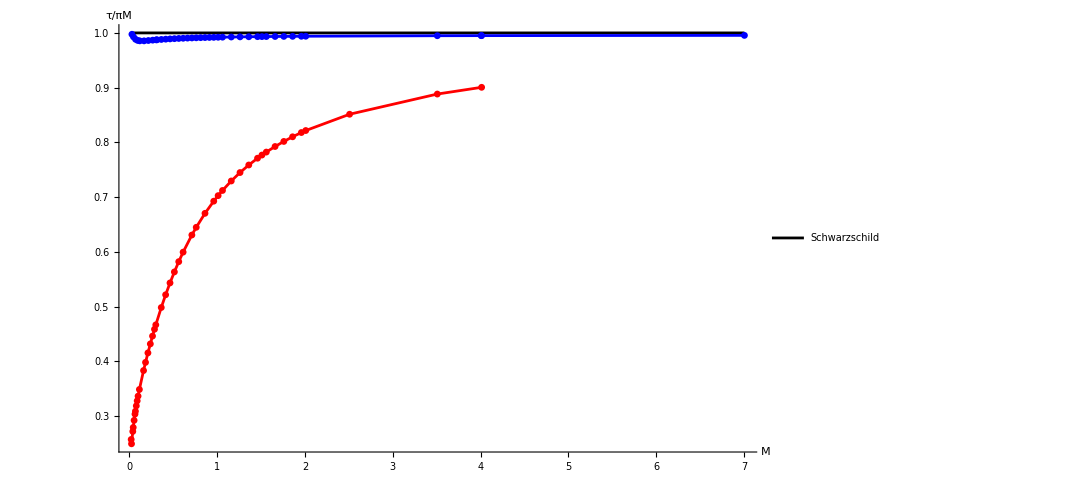

```mathematica
nH1T=ListPlot[Table[{dataT1[[i,2]],dataT1[[i,3]]/dataT1[[i,4]]},{i,Length[dataT1]}],Joined->True,PlotMarkers->{Automatic,Small},PlotStyle->Red,PlotLegends->Placed[{"Numerical Solution 2"},{0.75,0.3}]];
nH2T=ListPlot[Table[{dataT[[i,2]],dataT[[i,3]]/dataT[[i,4]]},{i,Length[dataT]}],Joined->True,PlotMarkers->{Automatic,Small},PlotStyle->Blue,PlotLegends->Placed[{"Numerical Solution 1"},{0.75,0.3}]];
nST=ListPlot[Table[{dataT[[i,2]],dataT[[i,4]]/dataT[[i,4]]},{i,Length[dataT]}],Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Schwarzschild"},{0.75,0.2}]];
nST1=ListPlot[Table[{dataT1[[i,2]],dataT1[[i,4]]/dataT1[[i,4]]},{i,Length[dataT1]}],Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Schwarzschild"},{0.75,0.2}]];
nNST=Show[nST,nH2T,nH1T,PlotRange->All,AxesLabel->{Style["M",FontSize->16],Style["τ/πM",FontSize->16]},ImageSize->800]
```

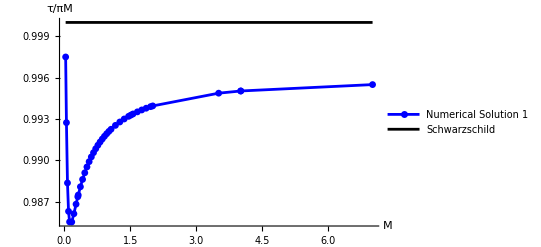

```mathematica
Show[nH2T,nST,PlotRange->All,AxesLabel->{Style["M",FontSize->16],Style["τ/πM",FontSize->16]}]
```

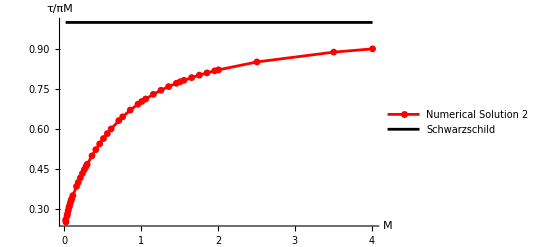

```mathematica
Show[nH1T,nST1,PlotRange->All,AxesLabel->{Style["M",FontSize->16],Style["τ/πM",FontSize->16]}]
```

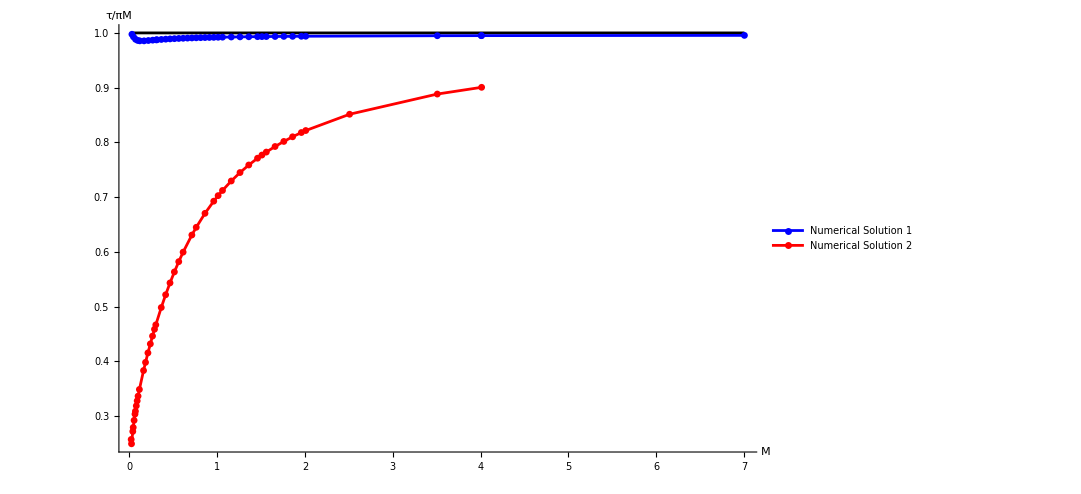

```mathematica
nH1T=ListPlot[Table[{dataT1[[i,2]],dataT1[[i,3]]/dataT1[[i,4]]},{i,Length[dataT1]}],Joined->True,PlotMarkers->{Automatic,Small},PlotStyle->Red,PlotLegends->Placed[{"Numerical Solution 2"},{0.8,0.2}]];
nH2T=ListPlot[Table[{dataT[[i,2]],dataT[[i,3]]/dataT[[i,4]]},{i,Length[dataT]}],Joined->True,PlotMarkers->{Automatic,Small},PlotStyle->Blue,PlotLegends->Placed[{"Numerical Solution 1"},{0.8,0.15}]];
nST=ListPlot[Table[{dataT[[i,2]],dataT[[i,4]]/dataT[[i,4]]},{i,Length[dataT]}],Joined->True,PlotStyle->Black];
nST1=ListPlot[Table[{dataT1[[i,2]],dataT1[[i,4]]/dataT1[[i,4]]},{i,Length[dataT1]}],Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Schwarzschild"},{0.8,0.2}]];
nNST=Show[nST,nH2T,nH1T,PlotRange->All,AxesLabel->{Style["M",FontSize->16],Style["τ/πM",FontSize->16]},ImageSize->800]
```